```mathematica
Differences[UnitConvert[Quantity["SpeedOfLight"]/(#),"Gigahertz"]&/@{Quantity[976.8,"Nanometers"],Quantity[976.8-0.3,"Nanometers"]}]
```

{94.2897 GHz}

I’m trying to model the dipolar interaction in two ways. One is to start with an array in the ground state, apply a pi/2, wait for a scanable time t, and apply a reverse pi/2. I then post select on sites that had pairs and try to see the dipolar interaction. Method two is to start in the ground state, apply a pi/2, wait for a scanable time t, and apply a forward pi/2 pulse (ie, phase pi). I then look at the average data without post-selecting.

Another question to answer is whether it makes sense to have an array in pairs or not in pairs. It seems like an equally spaced array will have a higher chance of having adjacent pairs, given that the chance of filling three molecules in a row is very low.

I need to take into account the fact that the probability range we work in is very low. This means that the spread of uncertainty is smaller.

### Setup

```mathematica
siteNumber=Length[arrayPos];
atomFilling=0.8;
feshbachFraction=0.3;
unblastedFraction=0.2;
stirapFraction=0.7;
badPrepFraction=0.3;
```

### Showing the statistics of the array

```mathematica
csLoading=RandomVariate[BernoulliDistribution[atomFilling],siteNumber];
naLoading=RandomVariate[BernoulliDistribution[atomFilling],siteNumber];
pairLoading=Times@@{csLoading,naLoading}ᵀ;
fbStep=pairLoading*RandomChoice[{feshbachFraction,1-feshbachFraction-badPrepFraction,badPrepFraction}->{fb,gh,bh},8]; (*feshbach, good hyperfine, bad hyperfine*)
fbLoading=fbStep/.{fb->1,gh->0,bh->0};
ghLoading=fbStep/.{fb->0,gh->1,bh->0};
ghubLoading=ghLoading*RandomVariate[BernoulliDistribution[unblastedFraction],siteNumber];
gsLoading=fbLoading*RandomVariate[BernoulliDistribution[stirapFraction],siteNumber];
imageLoading=gsLoading*RandomVariate[BernoulliDistribution[stirapFraction],siteNumber]+ghubLoading;
```

```mathematica
fillingA={};
Do[
csLoading=RandomVariate[BernoulliDistribution[atomFilling],siteNumber];
naLoading=RandomVariate[BernoulliDistribution[atomFilling],siteNumber];
pairLoading=Times@@{csLoading,naLoading}ᵀ;
fbStep=pairLoading*RandomChoice[{feshbachFraction,1-feshbachFraction-badPrepFraction,badPrepFraction}->{fb,gh,bh},8]; (*feshbach, good hyperfine, bad hyperfine*)
fbLoading=fbStep/.{fb->1,gh->0,bh->0};
ghLoading=fbStep/.{fb->0,gh->1,bh->0};
ghubLoading=ghLoading*RandomVariate[BernoulliDistribution[unblastedFraction],siteNumber];
gsLoading=fbLoading*RandomVariate[BernoulliDistribution[stirapFraction],siteNumber];
imageLoading=gsLoading*RandomVariate[BernoulliDistribution[stirapFraction],siteNumber]+ghubLoading;

AppendTo[fillingA,N[Mean[gsLoading]]];
,1000]
Mean[fillingA]
```

0.128875

### Array geometry

#### run anytime

```mathematica
nℋ1=2;
ℋ1=IdentityMatrix[nℋ1];
sℋ1=Partition[ℋ1,{nℋ1,1}]⟦1⟧;
lℋ1=Range[0,nℋ1-1];
s2lℋ1=AssociationThread[sℋ1->lℋ1];
l2sℋ1=AssociationThread[lℋ1->sℋ1];
σx=PauliMatrix[1];σy=PauliMatrix[2];σz=PauliMatrix[3];σp=1/2 (σx+ⅈ σy);σm=1/2 (σx-ⅈ σy);id=IdentityMatrix[2];σn=Cos[θ] σx+Sin[θ] σy;
(*arrayGeometry={1,0,1,0,0,1,0,1,0,0,1,0,1,0,0,1,0,1};*)
arrayGeometry={1,0,1,0,1,0,1,0,1,0,1,0,1,0,1};
arrayPos=Flatten[Position[arrayGeometry,1]];
ddℋn[{site1_,site2_,distance_}]:=1/distance^3(KroneckerProduct@@(ReplacePart[idArray,{site1->σp,site2->σm}])+KroneckerProduct@@(ReplacePart[idArray,{site1->σm,site2->σp}]));
fillingFraction=0.15;
tRange=Range[0,20000,500];
nTrials=100;
```

#### run in loop

```mathematica
fillings=ConstantArray[0,{siteNumber,Length[tRange],nTrials}];
Do[
siteFilling=RandomVariate[BernoulliDistribution[fillingFraction],siteNumber];
While[Total[siteFilling]==0,siteFilling=RandomVariate[BernoulliDistribution[fillingFraction],siteNumber];i++];
sitePos=Flatten[Position[siteFilling,1]];
nP=Length[sitePos];
siteDistances=Select[Flatten[Table[{i,j,5(arrayPos[[sitePos[[j]]]]-arrayPos[[sitePos[[i]]]])},{i,Range[nP]},{j,Range[nP]}],1],#[[3]]>0&];
If[nP<=1,finalFilling=siteFilling*RandomVariate[BernoulliDistribution[stirapFraction],siteNumber];,
nℋn=nℋ1^nP;
lℋn=Tuples[lℋ1,nP];
ℋn=IdentityMatrix[nℋn];
sℋn=Partition[ℋn,{nℋn,1}][[1]];
s2lℋn=AssociationThread[sℋn->lℋn];
l2sℋn=AssociationThread[lℋn->sℋn];
idArray=ConstantArray[id,nP];
σxℋn=Sum[KroneckerProduct@@ReplacePart[idArray,p->σx/2],{p,1,nP}];
numℋn[p_]:=KroneckerProduct@@ReplacePart[idArray,p->σp.σm];
σnℋn=Sum[KroneckerProduct@@ReplacePart[idArray,p->σn/2],{p,1,nP}];
numAvgℋn=Sum[numℋn[p]/nP,{p,1,nP}];
idℋn=KroneckerProduct@@idArray;
ψ0=KroneckerProduct@@ConstantArray[l2sℋ1[0],nP];
op1=N[σxℋn];
op2=N[idℋn+Total[ddℋn[#]&/@siteDistances]];
ψ=MatrixExp[ⅈ op1 π/2].MatrixExp[-ⅈ op2 tRange[[nt]]].MatrixExp[-ⅈ op1 π/2].ψ0;
nBySite=Table[Re[N[ψ†.numℋn[p].ψ]][[1,1]],{p,1,nP}];
finalFilling=imageEff*ReplacePart[siteFilling,Table[sitePos[[p]]->RandomVariate[BernoulliDistribution[nBySite[[p]]]],{p,1,nP}]];
];
fillings[[All,nt,trial]]=N[finalFilling];,{nt,1,Length[tRange]},{trial,1,nTrials}]
```

Increment::rvalue: i is not a variable with a value, so its value cannot be changed.

General::stop: Further output of Increment::rvalue will be suppressed during this calculation.

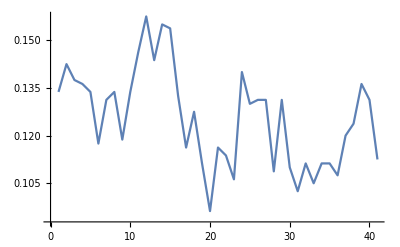

```mathematica
ListPlot[Table[Mean[Mean[fillings[[All,nt,All]]ᵀ]],{nt,Length[tRange]}],Joined->True]
```

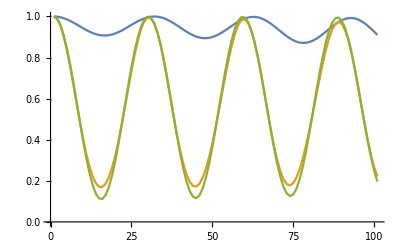

```mathematica
ListPlot[nBySiteOverTimeᵀ,Joined->True]
```

```mathematica
nBySiteOverTime[[20]][[2]]
```

0.322902

```mathematica
Length[tRange]
```

101

```mathematica
ntab0[[10]]
```

0.401463

```mathematica
op1=N[σxℋn];
op2=N[idℋn+Total[ddℋn[#]&/@siteDistances]]
```

KroneckerProduct::argmu: KroneckerProduct called with 1 argument; 2 or more arguments are expected.

General::stop: Further output of KroneckerProduct::argmu will be suppressed during this calculation.

{{1.+8.×10^-6 (KroneckerProduct[{{{0.,0.},{1.,0.}},{{0.,1.},{0.,0.}}}]+KroneckerProduct[{{{0.,1.},{0.,0.}},{{0.,0.},{1.,0.}}}]),8.×10^-6 (KroneckerProduct[{{{0.,0.},{1.,0.}},{{0.,1.},{0.,0.}}}]+KroneckerProduct[{{{0.,1.},{0.,0.}},{{0.,0.},{1.,0.}}}]),8.×10^-6 (KroneckerProduct[{{{0.,0.},{1.,0.}},{{0.,1.},{0.,0.}}}]+KroneckerProduct[{{{0.,1.},{0.,0.}},{{0.,0.},{1.,0.}}}]),8.×10^-6 (KroneckerProduct[{{{0.,0.},{1.,0.}},{{0.,1.},{0.,0.}}}]+KroneckerProduct[{{{0.,1.},{0.,0.}},{{0.,0.},{1.,0.}}}])},{8.×10^-6 (KroneckerProduct[{{{0.,0.},{1.,0.}},{{0.,1.},{0.,0.}}}]+KroneckerProduct[{{{0.,1.},{0.,0.}},{{0.,0.},{1.,0.}}}]),1.+8.×10^-6 (KroneckerProduct[{{{0.,0.},{1.,0.}},{{0.,1.},{0.,0.}}}]+KroneckerProduct[{{{0.,1.},{0.,0.}},{{0.,0.},{1.,0.}}}]),8.×10^-6 (KroneckerProduct[{{{0.,0.},{1.,0.}},{{0.,1.},{0.,0.}}}]+KroneckerProduct[{{{0.,1.},{0.,0.}},{{0.,0.},{1.,0.}}}]),8.×10^-6 (KroneckerProduct[{{{0.,0.},{1.,0.}},{{0.,1.},{0.,0.}}}]+KroneckerProduct[{{{0.,1.},{0.,0.}},{{0.,0.},{1.,0.}}}])},{8.×10^-6 (KroneckerProduct[{{{0.,0.},{1.,0.}},{{0.,1.},{0.,0.}}}]+KroneckerProduct[{{{0.,1.},{0.,0.}},{{0.,0.},{1.,0.}}}]),8.×10^-6 (KroneckerProduct[{{{0.,0.},{1.,0.}},{{0.,1.},{0.,0.}}}]+KroneckerProduct[{{{0.,1.},{0.,0.}},{{0.,0.},{1.,0.}}}]),1.+8.×10^-6 (KroneckerProduct[{{{0.,0.},{1.,0.}},{{0.,1.},{0.,0.}}}]+KroneckerProduct[{{{0.,1.},{0.,0.}},{{0.,0.},{1.,0.}}}]),8.×10^-6 (KroneckerProduct[{{{0.,0.},{1.,0.}},{{0.,1.},{0.,0.}}}]+KroneckerProduct[{{{0.,1.},{0.,0.}},{{0.,0.},{1.,0.}}}])},{8.×10^-6 (KroneckerProduct[{{{0.,0.},{1.,0.}},{{0.,1.},{0.,0.}}}]+KroneckerProduct[{{{0.,1.},{0.,0.}},{{0.,0.},{1.,0.}}}]),8.×10^-6 (KroneckerProduct[{{{0.,0.},{1.,0.}},{{0.,1.},{0.,0.}}}]+KroneckerProduct[{{{0.,1.},{0.,0.}},{{0.,0.},{1.,0.}}}]),8.×10^-6 (KroneckerProduct[{{{0.,0.},{1.,0.}},{{0.,1.},{0.,0.}}}]+KroneckerProduct[{{{0.,1.},{0.,0.}},{{0.,0.},{1.,0.}}}]),1.+8.×10^-6 (KroneckerProduct[{{{0.,0.},{1.,0.}},{{0.,1.},{0.,0.}}}]+KroneckerProduct[{{{0.,1.},{0.,0.}},{{0.,0.},{1.,0.}}}])}}

```mathematica
ψList={};Do[siteFilling=RandomVariate[BernoulliDistribution[fillingFraction],siteNumber];i=0;While[Total[siteFilling]==0,siteFilling=RandomVariate[BernoulliDistribution[fillingFraction],siteNumber];i++];
(*While[siteFilling[[{1,2}]]!={1,1},siteFilling=RandomVariate[BernoulliDistribution[fillingFraction],siteNumber];i++];*)
sitePos=Flatten[Position[siteFilling,1]];
fillingNumber=Length[sitePos];
siteDistances=Select[Flatten[Table[{i,j,5(arrayPos[[sitePos[[j]]]]-arrayPos[[sitePos[[i]]]])},{i,Range[fillingNumber]},{j,Range[fillingNumber]}],1],#[[3]]>0&];
nP=fillingNumber;
nℋn=nℋ1^nP;
lℋn=Tuples[lℋ1,nP];
ℋn=IdentityMatrix[nℋn];
sℋn=Partition[ℋn,{nℋn,1}][[1]];
s2lℋn=AssociationThread[sℋn->lℋn];
l2sℋn=AssociationThread[lℋn->sℋn];
idArray=If[nP==1,id,ConstantArray[id,nP]];
σxℋn=If[nP==1,σx/2,Sum[kp[ReplacePart[idArray,p->σx/2]],{p,1,nP}]];numℋn[p_]:=If[nP==1,σp.σm,kp[ReplacePart[idArray,p->σp.σm]]];
σnℋn=If[nP==1,σn/2,Sum[kp[ReplacePart[idArray,p->σn/2]],{p,1,nP}]];
numAvgℋn=Sum[numℋn[p]/nP,{p,1,nP}];
ddℋn[{site1_,site2_,distance_}]:=1/distance^3(kp[ReplacePart[idArray,{site1->σp,site2->σm}]]+kp[ReplacePart[idArray,{site1->σm,site2->σp}]]);
idℋn=kp[idArray];
ψ0=If[nP==1,l2sℋ1[0],kp[ConstantArray[l2sℋ1[0],nP]]];
op1=N[σxℋn];
op2=N[idℋn+Total[ddℋn[#]&/@siteDistances]];
(*op3=N[σnℋn];*)
tRange=Range[0,20000,200];
θRange=Range[0,2π,π/6];
ψtab0=ParallelTable[MatrixExp[ⅈ op1 π/2].MatrixExp[-ⅈ op2 t].MatrixExp[-ⅈ op1 π/2].ψ0,{t,tRange}];
ψtabπ=ParallelTable[MatrixExp[-ⅈ op1 π/2].MatrixExp[-ⅈ op2 t].MatrixExp[-ⅈ op1 π/2].ψ0,{t,tRange}];
(*ψtab0=ParallelTable[MatrixExp[ⅈ op3 π/2/.θ->0].MatrixExp[-ⅈ op2 t].MatrixExp[-ⅈ op1 π/2].ψ0,{θ,tRange}];
ψtabπ=ParallelTable[MatrixExp[ⅈ op3 π/2/.θ->π].MatrixExp[-ⅈ op2 t].MatrixExp[-ⅈ op1 π/2].ψ0,{θ,tRange}];*)
ntab0=ParallelTable[N[ψtab0[[j]]†.numAvgℋn.ψtab0[[j]]][[1,1]],{j,1,Length[tRange]}];
ntabπ=ParallelTable[N[ψtabπ[[j]]†.numAvgℋn.ψtabπ[[j]]][[1,1]],{j,1,Length[tRange]}];
(*ntab=ParallelTable[N[ψtab[[j]]†.numℋn[1].ψtab[[j]]][[1,1]],{j,1,Length[θRange]}];*)
AppendTo[ψList,ntab0-ntabπ],100
]
```

KroneckerProduct::argmu: KroneckerProduct called with 1 argument; 2 or more arguments are expected.

General::stop: Further output of KroneckerProduct::argmu will be suppressed during this calculation.

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

MatrixExp::matsq: Argument 0 at position 1 is not a non-empty square matrix.

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

MatrixExp::matsq: Argument 0 at position 1 is not a non-empty square matrix.

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable::nopar will be suppressed during this calculation.

MatrixExp::matsq: Argument 0. at position 1 is not a non-empty square matrix.

General::stop: Further output of MatrixExp::matsq will be suppressed during this calculation.

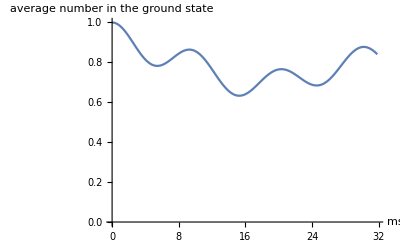

```mathematica
ListPlot[Transpose@{tRange/π 5 10^-3,Mean[ψList]},PlotRange->{0,1},Joined->True,AxesLabel->{"ms","average number\nin the ground state"}]
(*ListPlot[Transpose@{θRange,Mean[ψList]},PlotRange->{0,1},Joined->True,AxesLabel->{"ms","average number\nin the ground state"}]
siteFilling*)
```

# end

```mathematica
siteFilling=RandomVariate[BernoulliDistribution[0.2],siteNumber];i=0;While[Total[siteFilling]==0,siteFilling=RandomVariate[BernoulliDistribution[0.2],siteNumber];i++]
sitePos=Flatten[Position[siteFilling,1]];
fillingNumber=Length[sitePos];
siteDistances=Select[Flatten[Table[{i,j,5(arrayPos[[sitePos[[j]]]]-arrayPos[[sitePos[[i]]]])},{i,Range[fillingNumber]},{j,Range[fillingNumber]}],1],#[[3]]>0&]
```

{}

### States

#### Single particle

#### Multi-particle

```mathematica
nP=fillingNumber;
nℋn=nℋ1^nP;
lℋn=Tuples[lℋ1,nP];
ℋn=IdentityMatrix[nℋn];
sℋn=Partition[ℋn,{nℋn,1}][[1]];
s2lℋn=AssociationThread[sℋn->lℋn];
l2sℋn=AssociationThread[lℋn->sℋn];
```

### Operators

```mathematica
idArray=If[nP==1,id,ConstantArray[id,nP]];
σxℋn=If[nP==1,σx/2,Sum[kp[ReplacePart[idArray,p->σx/2]],{p,1,nP}]];numℋn[p_]:=If[nP==1,σp.σm,kp[ReplacePart[idArray,p->σp.σm]]];
numAvgℋn=Sum[numℋn[p]/nP,{p,1,nP}];
ddℋn[{site1_,site2_,distance_}]:=1/distance^3(kp[ReplacePart[idArray,{site1->σp,site2->σm}]]+kp[ReplacePart[idArray,{site1->σm,site2->σp}]])
idℋn=kp[idArray];
```

### Evolution

```mathematica
ψ0=If[nP==1,l2sℋ1[0],kp[ConstantArray[l2sℋ1[0],nP]]];
op1=N[σxℋn];
op2=N[idℋn+Total[ddℋn[#]&/@siteDistances]];
tRange=Range[0,5000,10];
```

```mathematica
ψtab=Table[MatrixExp[ⅈ op1 π/2].MatrixExp[-ⅈ op2 t].MatrixExp[-ⅈ op1 π/2].ψ0,{t,tRange}];
```

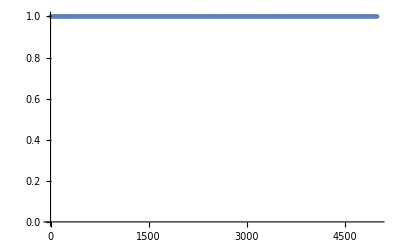

```mathematica
ListPlot[Table[{tRange[[j]],N[ψtab[[j]]†.numAvgℋn.ψtab[[j]]][[1,1]]},{j,1,Length[tRange]}],PlotRange->{0,1}]
```

The dipolar interaction at a distance of 1 has a pi time of π. The microwave pi time is also π. In the experiment the microwave pi time is order 5 us, whereas the dipolar interaction pi time is order 5 ms. The distance between two dipoles should therefore be 1000^(1/3)=10 so that the relative rates correspond.

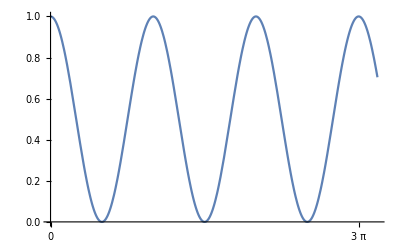

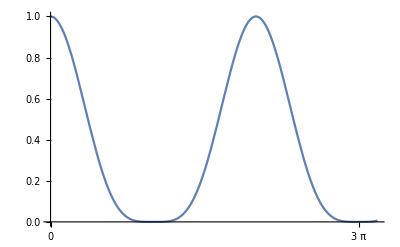

```mathematica
Plot[Abs[kp[{l2sℋ1[0],l2sℋ1[1]}]†.MatrixExp[-ⅈ ddℋn[{1,2,1}]t].kp[{l2sℋ1[0],l2sℋ1[1]}]]^2,{t,0,10},Ticks->{Range[0,10π,π],Automatic}]
Plot[Abs[kp[{l2sℋ1[0],l2sℋ1[0]}]†.MatrixExp[-ⅈ (kp[{id,σx/2}]+kp[{σx/2,id}])t].kp[{l2sℋ1[0],l2sℋ1[0]}]]^2,{t,0,10},Ticks->{Range[0,10π,π],Automatic}]
```

π is 5 us. t=100000 in the simulation is 160 ms.

```mathematica
20000/π*5 10^-3//N
```

31.831

31.831